# Animiranje grafov, vektorji in matrike

## Animiranje grafov

### Subsection. naloga:

```mathematica
Manipulate[Plot[a*Sin[k*x+n],{x,-5,5},PlotRange->{{-5,5},{-5,5}},AspectRatio->1],{a,-3,3},{k,-3,3},{n,-3,3}]
```

```mathematica
(* V funkciji Plot uporabite nastavitvi Range->{-5,5} in AspectRatio->Automatic *)
```

### Subsection. naloga:

Narišite graf premice y=k x+n  in na isti sliki še pravokotnico nanjo, ki gre skozi točko T(x_0,y_0) tako, da boste lahko spreminjali vrednosti parametrov k, n, x_0 in y_0. Na sliki označite z majhnim krogcem, kje leži točka T.
Namig: dva grafa na isti sliki narišete s funkcijo Plot tako, da predpisa podate v seznamu: {f[x], g[x]}.

```mathematica
(* Točko dodate z nastavitvijo Epilog->{PointSize[Large],Point[{{x0,y0}}]}] *)
Manipulate[Module[{f,g,xT=x0,yT=y0,kPerp,nPerp},(*premica*)f[x_]:=k*x+n;
(*smerni koeficient pravokotnice:-1/k*)kPerp=-1/k;
(*premica skozi T:y0=kPerp*x0+nPerp->nPerp=y0-kPerp*x0*)nPerp=y0-kPerp*x0;
(*pravokotnica*)g[x_]:=kPerp*x+nPerp;
Plot[{f[x],g[x]},{x,-10,10},PlotRange->{{-10,10},{-10,10}},Epilog->{Red,PointSize[0.02],Point[{x0,y0}]},AspectRatio->1]],{k,-5,5},{n,-10,10},{x0,-5,5},{y0,-5,5}]
```

### Subsection. naloga:

```mathematica
f[x_]:=x (x-2)^2/(x^2+1);
fprime[x_]:=D[f[x],x];  (*odvod*)

Manipulate[Module[{xT=x0,yT=f[x0],m=fprime[x0],(*smerni koeficient tangente*)tangent},tangent[x_]:=m (x-x0)+yT;
Plot[{f[x],tangent[x]},{x,-5,5},PlotRange->{{-5,5},{-5,5}},Epilog->{Red,PointSize[0.02],Point[{x0,yT}]},AspectRatio->1]],{x0,-4,6}]
```

D::ivar: -4 is not a valid variable.

D::ivar: -4. is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

D::ivar: 1.74 is not a valid variable.

### Subsection. naloga:

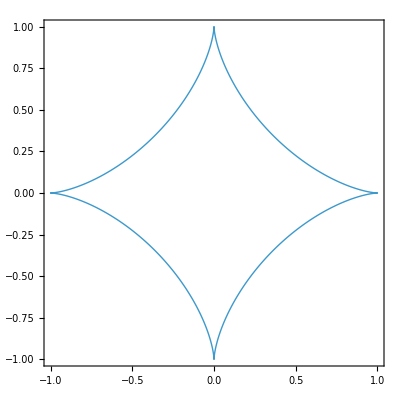

```mathematica
Manipulate[ContourPlot[Abs[x]^p+Abs[y]^p==1,{x,-1,1},{y,-1,1},PlotPoints->50,MaxRecursion->3,ContourStyle->Thick,PlotRange->{{-1,1},{-1,1}}],{p,0.1,4,0.01,Initialization:>(p=2)}]

ContourPlot[Abs[x]^(2/3)+Abs[y]^(2/3)==1,{x,-1,1},{y,-1,1},ContourStyle->Thick,PlotPoints->50,MaxRecursion->3]
```

## Vektorji in matrike

### Subsection. naloga:

```mathematica
(*1. Definicija vektorjev*)v1={1,2,3};
v2={-3,-2,5};

(*2. Skalarni produkt*)
dotProduct=v1.v2
(*Rezultat:1*(-3)+2*(-2)+3*5=-3-4+15=8*)

(*3. Vektorski produkt*)
crossProduct=Cross[v1,v2]
(*Rezultat:{2*5-3*(-2),3*(-3)-1*5,1*(-2)-2*(-3)}={10+6,-9-5,-2+6}={16,-14,4}*)

(*4. Dolžine vektorjev*)
normV1=Norm[v1]
(*sqrt(1^2+2^2+3^2)=Sqrt[14]*)

normV2=Norm[v2]
(*sqrt((-3)^2+(-2)^2+5^2)=Sqrt[38]*)

WhichLonger=If[normV1>normV2,"v1 je daljši","v2 je daljši"]
(*Rezultat:"v2 je daljši"*)

(*5. Enačba ravnine skozi točko (1,1,1) z normalo v smeri vektorskega produkta*)
p0={1,1,1};
normal=crossProduct;

planeEquation=normal.{x,y,z}-normal.p0==0
(*Izračun:16*(x-1)-14*(y-1)+4*(z-1)=0 Poenostavljeno:16 x-14 y+4 z-6=0*)

Simplify[planeEquation]
(*Končna enačba ravnine:16 x-14 y+4 z==6*)
```

8

{16,-14,4}

√14

√38

v2 je daljši

-6+16 x-14 y+4 z==0

3+7 y==8 x+2 z

### Subsection. naloga:

Naj bodo a⃗, b⃗ in c⃗ vektorji v R^3. S simboličnim računom dokaži identiteto  a⃗×(b⃗×c⃗)=(a⃗·c⃗)b⃗-(a⃗·b⃗)c⃗

### Subsection. naloga:

Dokaži, da za poljubni 2×2 matriki A in B velja enakost  (A B)^-1=B^-1 A^-1.

### Subsection. naloga:

```mathematica
(*1. Definicija matrike*)M={{9,2,-3},{3,2,1},{6,4,-1}};

(*2. Determinanta*)
detM=Det[M]
(*Rezultat:20*)

(*3. Lastne vrednosti*)
eigenvalues=Eigenvalues[M]
(*Rezultat:{10,2,-1}*)

(*4. Lastni vektorji*)
eigenvectors=Eigenvectors[M]
(*Rezultat (normalizirani niso nujni,lahko so poljubno skalirani):{{3,1,2},{-1,1,1},{1,2,3}}*)

(*5. Preverimo,ali je diagonalizabilna*)
MatrixRank[Transpose[eigenvectors]]==Length[M]
(*Rezultat:True,torej je matrika diagonalizabilna*)

(*6. Konstrukcija diagonalne in prehodne matrike*)
D=DiagonalMatrix[eigenvalues]
(*D={{10,0,0},{0,2,0},{0,0,-1}}*)

P=Transpose[eigenvectors]
(*P={{3,-1,1},{1,1,2},{2,1,3}}*)

Pinv=Inverse[P]
(*Pinv={{1/4,1/4,-1/4},{1/4,-3/4,1/4},{-1/4,1/4,1/4}}*)

(*7. Preverimo diagonalizabilnost*)
Simplify[P.D.Pinv==M]
(*Rezultat:True*)
```

-36

{3 (1+√2),4,3 (1-√2)}

{{-(-6-5 √2)/(6 (1+√2)),-(-2-√2)/(2 (1+√2)),1},{2,7,8},{-(-5+3 √2)/(3 √2 (-1+√2)),-(2-√2)/(2 (-1+√2)),1}}

True

Set::wrsym: Symbol D is Protected.

{{3 (1+√2),0,0},{0,4,0},{0,0,3 (1-√2)}}

{{-(-6-5 √2)/(6 (1+√2)),2,-(-5+3 √2)/(3 √2 (-1+√2))},{-(-2-√2)/(2 (1+√2)),7,-(2-√2)/(2 (-1+√2))},{1,8,1}}

{{(7+8/(-1+√2)-(4 √2)/(-1+√2))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(-2-8/(-1+√2)+(20 √2)/(3 (-1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(5/(-1+√2)-29/(3 √2 (-1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2)))},{(-1/(-1+√2)+1/(√2 (-1+√2))-1/(1+√2)-1/(√2 (1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(1/(-1+√2)-5/(3 √2 (-1+√2))+1/(1+√2)+5/(3 √2 (1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(2 √2)/(3 (-1+√2) (1+√2) (5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))))},{(-7+8/(1+√2)+(4 √2)/(1+√2))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(2-8/(1+√2)-(20 √2)/(3 (1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(5/(1+√2)+29/(3 √2 (1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2)))}}

{{1/6 (4+√2),2,1/6 (4-√2)},{1/(√2),7,-1/(√2)},{1,8,1}}.D.{{3/34 (8+7 √2),1/17 (-4+5 √2),1/34 (1-14 √2)},{-3/17,1/17,2/17},{-3/34 (-8+7 √2),1/17 (-4-5 √2),1/34 (1+14 √2)}}=={{9,2,-3},{3,2,1},{6,4,-1}}